```mathematica
Clear[genLapLine];
genLapLine[n_,freq_List,coups_List]:=Block[{w,c,appo},
w=Take[freq,n];
c=Take[coups,n-1];
appo = SparseArray[{Band[{2,1}]->c,Band[{1,1}]->w,Band[{1,2}]->c},{n,n}];
(*For[i=1,i≤nn, i++,
appo[[i,i]]=150 
];
*)
appo
]
```

## Negative chain

```mathematica
Clear[in];
in=Drop[Import[NotebookDirectory[]<>"examples/sd_neg_semi.tedopa"],1];
Clear[ωList,cList];
ωList=in[[All,2]]
cList =Drop[in[[All,1]],1]
```

{-0.424413,-0.486691,-0.495293,-0.497592,-0.498532,-0.499011,-0.499288,-0.499463,-0.49958,-0.499663,-0.499724,-0.499769,-0.499804,-0.499832,-0.499854,-0.499872,-0.499887,-0.4999,-0.49991,-0.499919,-0.499927,-0.499933,-0.499939,-0.499944,-0.499949,-0.499952,-0.499956,-0.499959,-0.499962,-0.499964,-0.499967,-0.499969,-0.499971,-0.499972,-0.499974,-0.499975,-0.499977,-0.499978,-0.499979,-0.49998,-0.499981,-0.499982,-0.499983,-0.499984,-0.499984,-0.499985,-0.499986,-0.499986,-0.499987,-0.499987,-0.499988,-0.499988,-0.499989,-0.499989,-0.49999,-0.49999,-0.49999,-0.499991,-0.499991,-0.499991,-0.499991,-0.499992,-0.499992,-0.499992,-0.499993,-0.499993,-0.499993,-0.499993,-0.499993,-0.499994,-0.499994,-0.499994,-0.499994,-0.499994,-0.499994,-0.499995,-0.499995,-0.499995,-0.499995,-0.499995,-0.499995,-0.499995,-0.499995,-0.499996,-0.499996,-0.499996,-0.499996,-0.499996,-0.499996,-0.499996,-0.499996,-0.499996,-0.499996,-0.499996,-0.499996,-0.499997,-0.499997,-0.499997,-0.499997,-0.499997}

{0.264336,0.2537,0.251634,0.250925,0.250597,0.250417,0.250308,0.250236,0.250187,0.250152,0.250126,0.250106,0.250091,0.250078,0.250068,0.25006,0.250053,0.250047,0.250043,0.250039,0.250035,0.250032,0.250029,0.250027,0.250025,0.250023,0.250021,0.25002,0.250018,0.250017,0.250016,0.250015,0.250014,0.250013,0.250013,0.250012,0.250011,0.250011,0.25001,0.25001,0.250009,0.250009,0.250008,0.250008,0.250008,0.250007,0.250007,0.250007,0.250006,0.250006,0.250006,0.250006,0.250006,0.250005,0.250005,0.250005,0.250005,0.250005,0.250004,0.250004,0.250004,0.250004,0.250004,0.250004,0.250004,0.250004,0.250003,0.250003,0.250003,0.250003,0.250003,0.250003,0.250003,0.250003,0.250003,0.250003,0.250003,0.250003,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002}

```mathematica
Length[ωList]
Length[cList]
```

100

99

```mathematica
Clear[nn];
nn=100
```

100

```mathematica
genLapLine[10,ωList,cList]//MatrixForm
```

(-0.424413 | 0.264336 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.264336 | -0.486691 | 0.2537 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.2537 | -0.495293 | 0.251634 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.251634 | -0.497592 | 0.250925 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.250925 | -0.498532 | 0.250597 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.250597 | -0.499011 | 0.250417 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.250417 | -0.499288 | 0.250308 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.250308 | -0.499463 | 0.250236 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.250236 | -0.49958 | 0.250187
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.250187 | -0.499663)

### Exact

```mathematica
Clear[x0];
x0=Table[KroneckerDelta[i,1],{i,1,nn}];
```

```mathematica
Clear[unknown];
unknown  = Table[p[i][t],{i,1,nn}];
```

```mathematica
Clear[lap];
lap=genLapLine[nn,ωList,cList];
```

```mathematica
Clear[appo];
appo = -ⅈ *lap.unknown;
```

```mathematica
Clear[equations];
equations = Table[D[p[i][t],t]== appo[[i]],{i,1,nn}];
```

```mathematica
equations[[1]]
```

p[1]'[t]==-ⅈ (-0.424413 p[1][t]+0.264336 p[2][t])

```mathematica
Clear[init];
init=Table[p[i][0.]==x0[[i]],{i,1,nn}];
```

```mathematica
Clear[problem];
problem = Join[equations,init];
```

```mathematica
Clear[qsolution];
qsolution = NDSolve[problem,unknown,{t,0,1}][[1]];
```

```mathematica
(*Manipulate[
Show[
ListPlot[Abs[unknown]^2/.qsolution/.t->tt,PlotRange->{0,1}],
ListPlot[Abs[unknown]^2/.qsolution/.t->tt,PlotRange->{0,1},Joined->True,PlotStyle->Red]
]
,{tt,0,1}]*)
```

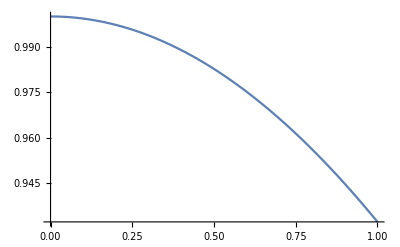

```mathematica
Plot[Abs[p[1][t]]^2/.qsolution/.t->(tt),{tt,0,1}]
```

```mathematica
Clear[data];
data = Import[NotebookDirectory[]<>"examples/test_tedopa_measurements_add.dat"];
```

```mathematica
Clear[which,szNeg];
which = Position[data[[1]],"Sz_30"][[1,1]];
szNeg = Table[{data[[i]][[1]],data[[i]][[which]]},{i,2,Length[data]}]
```

{{0.01,-0.499993},{0.02,-0.499972},{0.03,-0.499937},{0.04,-0.499888},{0.05,-0.499825},{0.06,-0.499748},{0.07,-0.499658},{0.08,-0.499553},{0.09,-0.499434},{0.1,-0.499301},{0.11,-0.499155},{0.12,-0.498994},{0.13,-0.49882},{0.14,-0.498631},{0.15,-0.498429},{0.16,-0.498213},{0.17,-0.497982},{0.18,-0.497738},{0.19,-0.49748},{0.2,-0.497208},{0.21,-0.496923},{0.22,-0.496623},{0.23,-0.496309},{0.24,-0.495982},{0.25,-0.495641},{0.26,-0.495286},{0.27,-0.494917},{0.28,-0.494534},{0.29,-0.494138},{0.3,-0.493728},{0.31,-0.493304},{0.32,-0.492866},{0.33,-0.492415},{0.34,-0.49195},{0.35,-0.491471},{0.36,-0.490978},{0.37,-0.490472},{0.38,-0.489952},{0.39,-0.489419},{0.4,-0.488872},{0.41,-0.488311},{0.42,-0.487737},{0.43,-0.487149},{0.44,-0.486548},{0.45,-0.485933},{0.46,-0.485305},{0.47,-0.484663},{0.48,-0.484008},{0.49,-0.48334},{0.5,-0.482658},{0.51,-0.481962},{0.52,-0.481254},{0.53,-0.480532},{0.54,-0.479796},{0.55,-0.479048},{0.56,-0.478286},{0.57,-0.477511},{0.58,-0.476722},{0.59,-0.475921},{0.6,-0.475106},{0.61,-0.474279},{0.62,-0.473438},{0.63,-0.472584},{0.64,-0.471717},{0.65,-0.470837},{0.66,-0.469945},{0.67,-0.469039},{0.68,-0.46812},{0.69,-0.467189},{0.7,-0.466244},{0.71,-0.465287},{0.72,-0.464317},{0.73,-0.463335},{0.74,-0.462339},{0.75,-0.461331},{0.76,-0.46031},{0.77,-0.459277},{0.78,-0.458231},{0.79,-0.457173},{0.8,-0.456102},{0.81,-0.455019},{0.82,-0.453923},{0.83,-0.452815},{0.84,-0.451694},{0.85,-0.450561},{0.86,-0.449416},{0.87,-0.448259},{0.88,-0.447089},{0.89,-0.445908},{0.9,-0.444714},{0.91,-0.443508},{0.92,-0.44229},{0.93,-0.44106},{0.94,-0.439819},{0.95,-0.438565},{0.96,-0.437299},{0.97,-0.436022},{0.98,-0.434733},{0.99,-0.433432},{1.,-0.432119}}

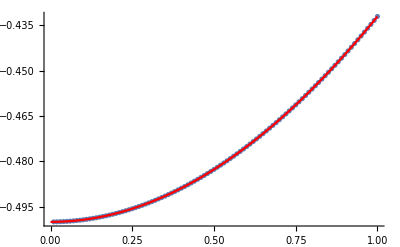

```mathematica
Show[
ListPlot[szNeg],
Plot[1/2 -Abs[p[1][t]]^2/.qsolution/.t->(tt),{tt,0,1},PlotStyle->Red],
PlotRange->All
]
```

## Positive chain

```mathematica
Clear[in];
in=Drop[Import[NotebookDirectory[]<>"examples/sd_pos_semi.tedopa"],1];
Clear[ωList,cList];
ωList=in[[All,2]]
cList = Drop[in[[All,1]],1]
```

{0.424413,0.486691,0.495293,0.497592,0.498532,0.499011,0.499288,0.499463,0.49958,0.499663,0.499724,0.499769,0.499804,0.499832,0.499854,0.499872,0.499887,0.4999,0.49991,0.499919,0.499927,0.499933,0.499939,0.499944,0.499949,0.499952,0.499956,0.499959,0.499962,0.499964,0.499967,0.499969,0.499971,0.499972,0.499974,0.499975,0.499977,0.499978,0.499979,0.49998,0.499981,0.499982,0.499983,0.499984,0.499984,0.499985,0.499986,0.499986,0.499987,0.499987,0.499988,0.499988,0.499989,0.499989,0.49999,0.49999,0.49999,0.499991,0.499991,0.499991,0.499991,0.499992,0.499992,0.499992,0.499993,0.499993,0.499993,0.499993,0.499993,0.499994,0.499994,0.499994,0.499994,0.499994,0.499994,0.499995,0.499995,0.499995,0.499995,0.499995,0.499995,0.499995,0.499995,0.499996,0.499996,0.499996,0.499996,0.499996,0.499996,0.499996,0.499996,0.499996,0.499996,0.499996,0.499996,0.499997,0.499997,0.499997,0.499997,0.499997}

{0.264336,0.2537,0.251634,0.250925,0.250597,0.250417,0.250308,0.250236,0.250187,0.250152,0.250126,0.250106,0.250091,0.250078,0.250068,0.25006,0.250053,0.250047,0.250043,0.250039,0.250035,0.250032,0.250029,0.250027,0.250025,0.250023,0.250021,0.25002,0.250018,0.250017,0.250016,0.250015,0.250014,0.250013,0.250013,0.250012,0.250011,0.250011,0.25001,0.25001,0.250009,0.250009,0.250008,0.250008,0.250008,0.250007,0.250007,0.250007,0.250006,0.250006,0.250006,0.250006,0.250006,0.250005,0.250005,0.250005,0.250005,0.250005,0.250004,0.250004,0.250004,0.250004,0.250004,0.250004,0.250004,0.250004,0.250003,0.250003,0.250003,0.250003,0.250003,0.250003,0.250003,0.250003,0.250003,0.250003,0.250003,0.250003,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002,0.250002}

```mathematica
Length[ωList]
Length[cList]
```

100

99

```mathematica
Clear[nn];
nn=100
```

100

```mathematica
genLapLine[10,ωList,cList]//MatrixForm
```

(0.424413 | 0.264336 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.264336 | 0.486691 | 0.2537 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.2537 | 0.495293 | 0.251634 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.251634 | 0.497592 | 0.250925 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.250925 | 0.498532 | 0.250597 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.250597 | 0.499011 | 0.250417 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.250417 | 0.499288 | 0.250308 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.250308 | 0.499463 | 0.250236 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.250236 | 0.49958 | 0.250187
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.250187 | 0.499663)

### Exact

```mathematica
Clear[x0];
x0=Table[KroneckerDelta[i,1],{i,1,nn}];
```

```mathematica
Clear[unknown];
unknown  = Table[p[i][t],{i,1,nn}];
```

```mathematica
Clear[lap];
lap=genLapLine[nn,ωList,cList];
```

```mathematica
Clear[appo];
appo = -ⅈ *lap.unknown;
```

```mathematica
Clear[equations];
equations = Table[D[p[i][t],t]== appo[[i]],{i,1,nn}];
```

```mathematica
equations[[1]]
```

p[1]'[t]==-ⅈ (0.424413 p[1][t]+0.264336 p[2][t])

```mathematica
Clear[init];
init=Table[p[i][0.]==x0[[i]],{i,1,nn}];
```

```mathematica
Clear[problem];
problem = Join[equations,init];
```

```mathematica
Clear[qsolution];
qsolution = NDSolve[problem,unknown,{t,0,1}][[1]];
```

```mathematica
(*Manipulate[
Show[
ListPlot[Abs[unknown]^2/.qsolution/.t->tt,PlotRange->{0,1}],
ListPlot[Abs[unknown]^2/.qsolution/.t->tt,PlotRange->{0,1},Joined->True,PlotStyle->Red]
]
,{tt,0,1}]*)
```

```mathematica
Plot[Abs[p[1][t]]^2/.qsolution/.t->(tt),{tt,0,1}]
```

-Graphics-

```mathematica
Clear[data];
data = Import[NotebookDirectory[]<>"examples/test_tedopa_measurements_add.dat"];
```

```mathematica
Clear[which,szPos];
which = Position[data[[1]],"Sz_32"][[1,1]];
szPos = Table[{data[[i]][[1]],data[[i]][[which]]},{i,2,Length[data]}];
```

```mathematica
szPos;
```

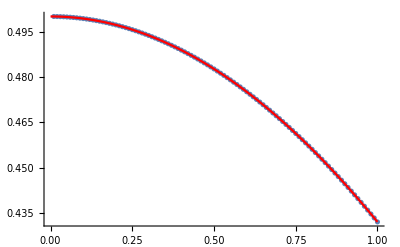

```mathematica
Show[
ListPlot[szPos],
Plot[-1/2 +Abs[p[1][t]]^2/.qsolution/.t->(tt),{tt,0,1},PlotStyle->Red],
PlotRange->All
]
```